```mathematica
Clear[lcoo,lcoot1,lcoot2,lcoot3,p,lm,lpagg,lpagg1,duads,lnaus,genTuCox,genPerm,genRiflex];
```

```mathematica
(*
	Questa funzione disegna un grafo detto di Tutte_Coxeter.

	Questo grafo ha 30 nodi: 15 corrispondono ai duads di {1,2,3,4,5,6} 15 corrispondono ai sinthemes (partizioni di {1,2,3,4,5,6} in 3 duads)
	I lati del grafo congiungono i nodi relativi ai duads ai nodi relativi ai synthemes cui appartengono.
	Gli automorfismi (cioe' le simmetrie) di questo grafo formano un gruppo che e' isomorfo al gruppo degli automorfismi di S6
		che ricordiamo ha 1440 elementi essendo il prodotto diretto di Inn(S6)xOut(S6) dove Inn(S6) e' isomorfo a S6 e Out(S6) e' isomorfo a C2

INPUT: prm permutazione dei 30 nodi (default la permutazione identica)
	   cx  coordinata X del centro del grafo (default 0)
	   nfs rotazione del grafo. Viene realizzata una rotazione in senso antiorario di angolo nsf*(12 gradi)
		   Se nfs e' intero questo corrisponde ad una rotazione dei nodi.
OUTPUT: Elemento da graficare
     
*)
genTuCox[prm_:{0},cx_:0,nfs_:0]:=(
clr1=Black;
clr2=Green;
cy=0;
r=10;
dfs=Pi/2+Pi/30;
da=2Pi/30;
If[prm[[1]]==0,perm=Range[30],perm=prm];

lcoo=Range[30];
lcoot1=Range[30];
lcoot2=Range[30];
lcoot3=Range[30];
ang=0;
offs1=2;
offs2=4;
offs3=6;
fs=Pi/15 nfs;
For[k=1,k≤30,k++,
pp={cx+r Cos[ang+dfs+fs],cy+r Sin[ang+dfs+fs]};
lcoo[[perm[[k]]]]=pp;
lcoot1[[perm[[k]]]]={pp[[1]]+offs1 Cos[ang+dfs+fs],pp[[2]]+offs1 Sin[ang+dfs+fs] };
lcoot2[[perm[[k]]]]={pp[[1]]+offs2 Cos[ang+dfs+fs],pp[[2]]+offs2 Sin[ang+dfs+fs] };
lcoot3[[perm[[k]]]]={pp[[1]]+offs3 Cos[ang+dfs+fs],pp[[2]]+offs3 Sin[ang+dfs+fs] };
ang-=da
];

lpagg1=List[14,19,24,11,28,15,20,25,30,17,4,21,26,1,6,23,10,27,2,7,12,29,16,3,8,13,18,5,22,9];
duads=List[12,13,14,15,16,23,24,25,26,34,35,36,45,46,56];
colors={"Red","Blue"};
p=Range[30];
sizep=10;
For[k=1,k≤30,k+=2,
p[[k]]={AbsolutePointSize[sizep],RGBColor[colors[[Mod[k-1,2]+1]]],Point[lcoo[[k]]],Text[duads[[Floor[k/2]+1]],lcoot1[[k]]]}
];
For[k=2,k≤30,k+=2,
p[[k]]={AbsolutePointSize[sizep],RGBColor[colors[[Mod[k-1,2]+1]]],Point[lcoo[[k]]],Text[duads[[Mod[Floor[(k-2)/2],15]+1]],lcoot1[[k]]],Text[duads[[Mod[Floor[k/2],15]+1]],lcoot2[[k]]],Text[duads[[Floor[lpagg1[[k]]/2+1]]],lcoot3[[k]]]}
];

ln=Range[30];
For[k=1,k≤29,k++,
ln[[k]]=Line[{lcoo[[k]],lcoo[[k+1]]}]
];
ln[[30]]=Line[{lcoo[[30]],lcoo[[1]]}];

lpagg=List[{1,14},{2,19},{3,24},{4,11},{5,28},{6,15},{7,20},{8,25},{9,30},{10,17},{12,21},{13,26},{16,23},{18,27},{22,29}];
lnaus=Range[15];
For[k=1,k≤15,k++,
lnaus[[k]]=Line[{lcoo[[lpagg[[k]][[1]]]],lcoo[[lpagg[[k]][[2]]]]}]
];

Return[{p,{clr1,ln},{clr2,lnaus}}];
)

(*
	Questa funzione applica una serie di trasposizioni ad una permutazione di partenza

	INPUT: per insieme delle trasposizioni da applicare
		 n   numero di elementi della permutazione di partenza
		 prm permutazione di partenza (default la permutazione identica su n elementi)
*)
genPerm[per_,n_,prm_:{0}]:=(
If[prm[[1]]==0,result=Range[n],result=prm];
nel1=Length[per];
For[k1=1,k1≤nel1,k1++,
nel2=Length[per[[k1]]];
For[k2=nel2,k2>=1,k2--,
inda=per[[k1]][[k2]];
If[k2<nel2,result[[indp]]=result[[inda]],appo=result[[inda]]];
indp=inda;
];
result[[indp]]=appo;
];
Return[result];
)

(*
	Questa funzione applica una riflessione ad una permutazione iniziale di vertici
   La riflessione e' effettuata rispetto ad un asse che passa per il vertice v1
   se v1=v2 o passa per la mediana del lato che congiunge v1 a v2 (dovra' essere v2=(v1+1 modulo n) 

	INPUT: v1  primo vertice
		 v2  secondo vertice
		 n   numero dei vertici
		 prm permutazione iniziale di n vertici
*)
genRiflex[v1_,v2_,n_,prm_:{0}]:=(
If[prm[[1]]==0,result=Range[n],result=prm];
If[v1==v2,
v=v1;
For[k=1,k≤Floor[(n-1)/2],k++,
appo=result[[Mod[v-1-k,n]+1]];
result[[Mod[v-1-k,n]+1]]=result[[Mod[v-1+k,n]+1]];
result[[Mod[v-1+k,n]+1]]=appo
],
For[k=1,k≤Floor[n/2],k++,
appo=result[[Mod[v1-k,n]+1]];
result[[Mod[v1-k,n]+1]]=result[[Mod[v2+k-2,n]+1]];
result[[Mod[v2+k-2,n]+1]]=appo
]
];
Return[result];
)
```

```mathematica
gen1={{5,11},{6, 10},{7, 17},{8 ,16},{9, 15},{12, 28},{13, 29},{14, 30},{18, 20},{21, 27},{22, 26},{23 ,25}};
gen2={{5,11},{6, 12},{7, 21},{8 ,22},{9, 29},{10, 28},{13, 15},{16, 26},{17, 27},{23, 25}};
gen3={{2,14},{3, 15},{4, 6},{7 ,11},{8, 10},{12, 20},{13, 19},{16, 24},{17, 25},{18, 26}};
gen4={{1,2,3, 4,5, 6,7 ,8,9, 30},{10, 29,14, 19,24, 11,28, 15,20, 25},{12, 27,16 ,21,26,17,22,13,18,23}};
```

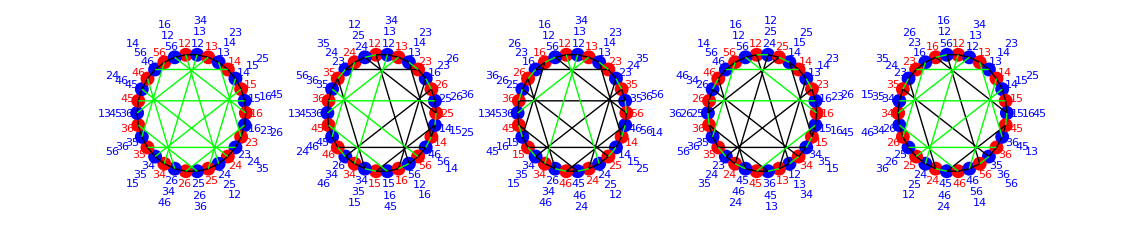

```mathematica
g1=genTuCox[];
g2=genTuCox[genPerm[gen1,30],35];
g3=genTuCox[genPerm[gen2,30],70];
g4=genTuCox[genPerm[gen3,30],105];
g5=genTuCox[genPerm[gen4,30],140];
Graphics[{g1,g2,g3,g4,g5}]
```

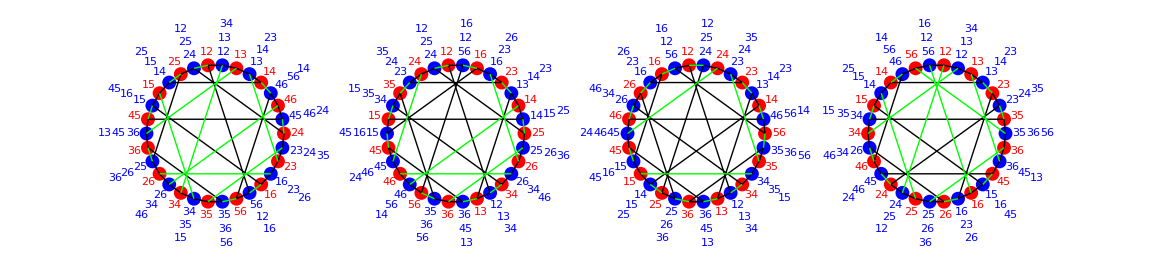

```mathematica
g6=genTuCox[genPerm[gen2,30,genPerm[gen1,30]]];
g7=genTuCox[genPerm[gen3,30,genPerm[gen1,30]],35];
g8=genTuCox[genPerm[gen3,30,genPerm[gen2,30]],70];
g9=genTuCox[genPerm[gen4,30,genPerm[gen2,30]],105];
Graphics[{g6,g7,g8,g9}]
```

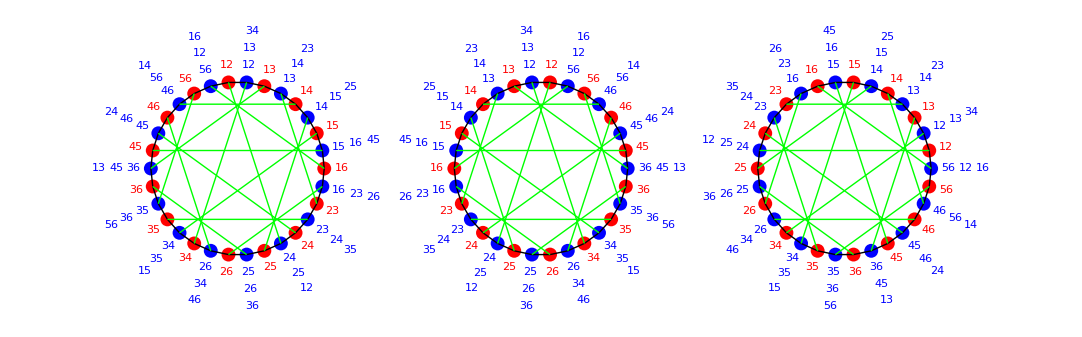

```mathematica
g1=genTuCox[];
g2=genTuCox[genRiflex[1,2,30],35];
g3=genTuCox[genRiflex[4,5,30],70];
Graphics[{g1,g2,g3}]
```

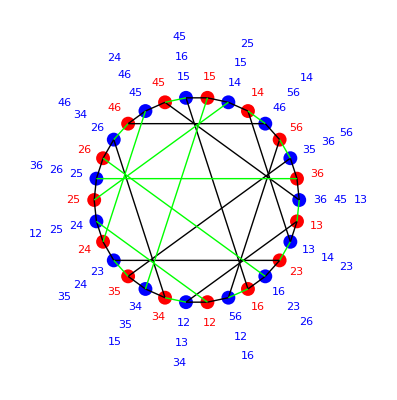

```mathematica
Graphics[{genTuCox[genPerm[gen1,30,genRiflex[4,5,30]]]}]
```

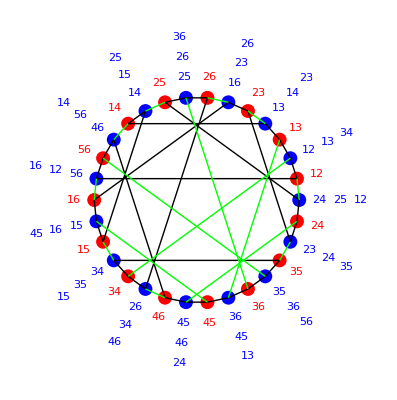

```mathematica
Graphics[{genTuCox[genRiflex[4,5,30,genPerm[gen1,30]]]}]
```

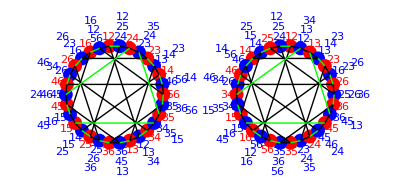

```mathematica
genPerm[gen3,30,genPerm[gen2,30]];
genPerm[gen4,30,genPerm[gen1,30]];
g8=genTuCox[genPerm[gen3,30,genPerm[gen2,30]]];
g9=genTuCox[genPerm[gen4,30,genPerm[gen1,30]],35];
Graphics[{g8,g9}]
```

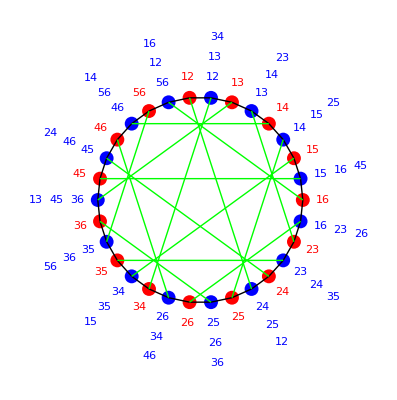

```mathematica
g1=genTuCox[];
Graphics[{g1}]
```